```mathematica
With[
{sets=allGraphs4},
Sort[Tally[Table[Length[ListofVars[sets[k,"colofourrealnull"]]],{k,Sort[Select[Keys[sets],VertexCount[sets[#,"graph"]]==4&]]}]]]
]
```

{{1,1},{2,6},{4,15},{5,4},{8,16},{10,12},{12,3},{13,6},{15,1}}

```mathematica
With[
{sets=allGraphs5},
Sort[Tally[Table[Length[ListofVars[sets[k,"colofour"]]],{k,Sort[Select[Keys[sets],VertexCount[sets[#,"graph"]]==5&]]}]]]
]
```

{{1,1},{2,10},{3,30},{4,35},{5,75},{6,30},{7,135},{8,60},{9,30},{10,160},{11,12},{12,60},{13,70},{15,125},{16,15},{17,10},{20,110},{27,45},{37,10},{52,1}}

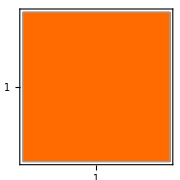
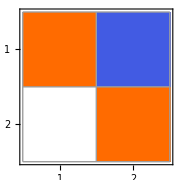
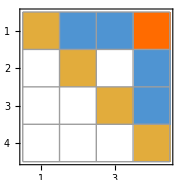
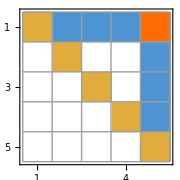
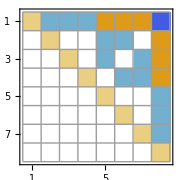
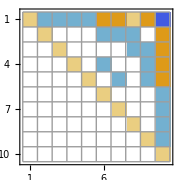
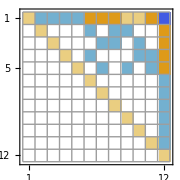
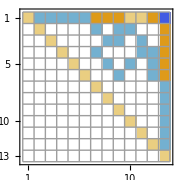
{-Graphics-{-Graphics-034,1},-Graphics-{-Graphics-121,10},-Graphics-{-Graphics-416,45},-Graphics-{-Graphics-138,10},-Graphics-{-Graphics-3112,110},-Graphics-{-Graphics-406,70},-Graphics-{-Graphics-1209,15},-Graphics-{-Graphics-1213,30},-Graphics-{-Graphics-3640,75},-Graphics-{-Graphics-7608,125},-Graphics-{-Graphics-7694,160},-Graphics-{-Graphics-8496,60},-Graphics-{-Graphics-8502,135},-Graphics-{-Graphics-10930,35},-Graphics-{-Graphics-31954,12},-Graphics-{-Graphics-31962,60},-Graphics-{-Graphics-32792,30},-Graphics-{-Graphics-32800,30},-Graphics-{-Graphics-98410,10},-Graphics-{-Graphics-295240,1}}

```mathematica
Map[
Labeled[MatrixPlot[MobiusMatrixFromSets[Map[SymbolToSets,Sort[ListofVars[allGraphs5[#[[1]],"colofourrealnull"]],CompareSymbols]]],Mesh->All, ImageSize->180],{ShowGraph5Least[#[[1]]],#[[2]]}]&,
With[
{sets=allGraphs5},
Sort[Tally[Table[k,{k,Sort[Select[Keys[sets],VertexCount[sets[#,"graph"]]==5&]]}],Length[ListofVars[sets[#1,"colofour"]]]==Length[ListofVars[sets[#2,"colofour"]]]&]]
]
]
```

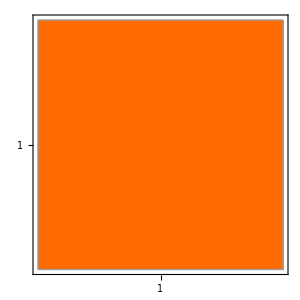
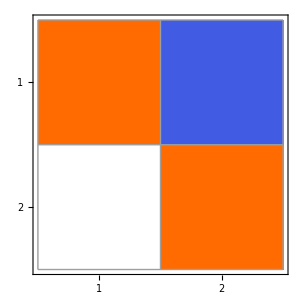
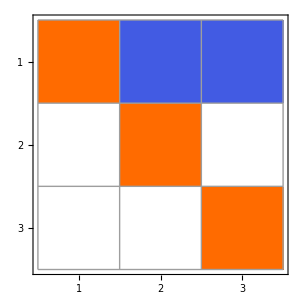
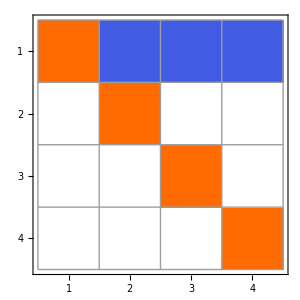
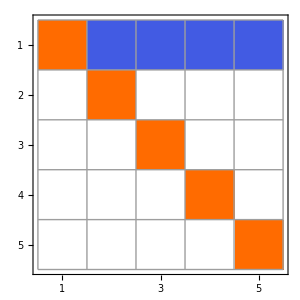
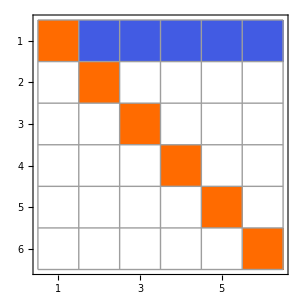
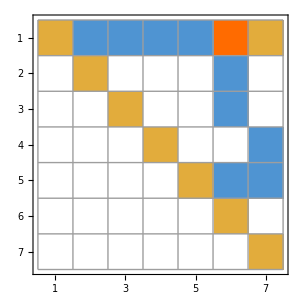
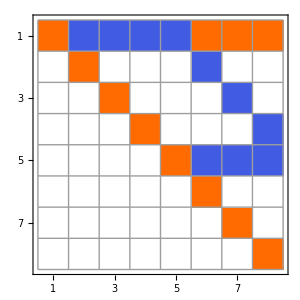
{-Graphics-{-Graphics-7174453,1},-Graphics-{-Graphics-2391484,15},-Graphics-{-Graphics-797161,60},-Graphics-{-Graphics-265720,105},-Graphics-{-Graphics-88573,230},-Graphics-{-Graphics-29524,186},-Graphics-{-Graphics-246037,585},-Graphics-{-Graphics-265719,435},-Graphics-{-Graphics-68890,390},-Graphics-{-Graphics-239476,1140},-Graphics-{-Graphics-9841,492},-Graphics-{-Graphics-246028,720},-Graphics-{-Graphics-62329,1320},-Graphics-{-Graphics-246036,405},-Graphics-{-Graphics-239233,1275},-Graphics-{-Graphics-3280,990},-Graphics-{-Graphics-60142,1620},-Graphics-{-Graphics-790515,60},-Graphics-{-Graphics-246027,360},-Graphics-{-Graphics-9832,2640},-Graphics-{-Graphics-1093,315},-Graphics-{-Graphics-239392,1440},-Graphics-{-Graphics-62328,900},-Graphics-{-Graphics-243846,360},-Graphics-{-Graphics-3037,790},-Graphics-{-Graphics-364,15},-Graphics-{-Graphics-59899,2700},-Graphics-{-Graphics-3279,630},-Graphics-{-Graphics-62245,1995},-Graphics-{-Graphics-239391,180},-Graphics-{-Graphics-850,1090},-Graphics-{-Graphics-62085,300},-Graphics-{-Graphics-59818,2160},-Graphics-{-Graphics-3196,360},-Graphics-{-Graphics-62244,360},-Graphics-{-Graphics-243810,60},-Graphics-{-Graphics-59898,1080},-Graphics-{-Graphics-121,90},-Graphics-{-Graphics-3036,60},-Graphics-{-Graphics-769,1140},-Graphics-{-Graphics-3195,72},-Graphics-{-Graphics-59809,1296},-Graphics-{-Graphics-849,405},-Graphics-{-Graphics-40,240},-Graphics-{-Graphics-760,1080},-Graphics-{-Graphics-120,45},-Graphics-{-Graphics-13,20},-Graphics-{-Graphics-31,435},-Graphics-{-Graphics-4,105},-Graphics-{-Graphics-1,15},-Graphics-{-Graphics-0,1}}

```mathematica
With[{sets=allGraphs6, max=6,colofour="colofour"},Map[
Labeled[MatrixPlot[MobiusMatrixFromSets[Map[SymbolToSets,Sort[ListofVars[sets[#[[1]],colofour]],CompareSymbols]]],Mesh->All, ImageSize->300],{Labeled[sets[#[[1]],"graph"],#[[1]]],#[[2]]}]&,
Sort[Tally[Table[k,{k,Sort[Select[Keys[sets],VertexCount[sets[#,"graph"]]==max&]]}],Length[ListofVars[sets[#1,colofour]]]==Length[ListofVars[sets[#2,colofour]]]&],Length[ListofVars[sets[#1[[1]],colofour]]]<Length[ListofVars[sets[#2[[1]],colofour]]]&]
]
]
```

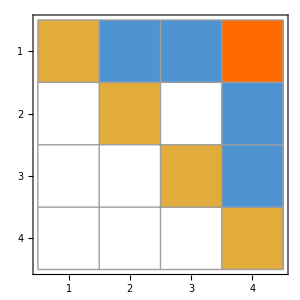
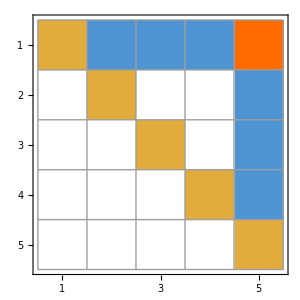
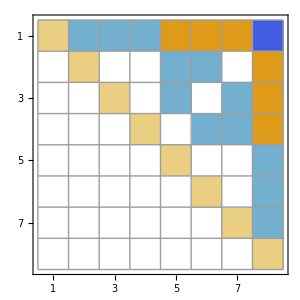
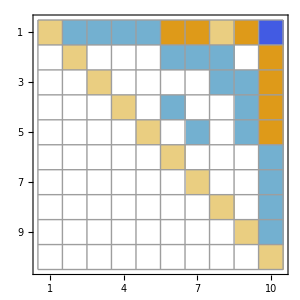
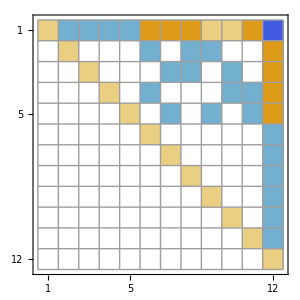
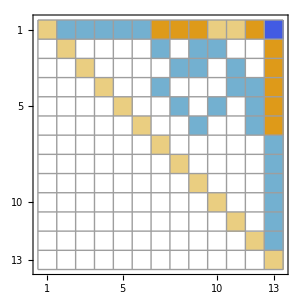
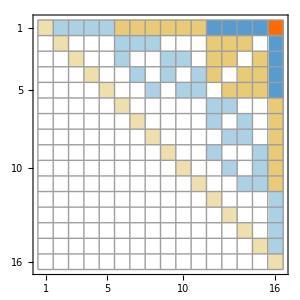
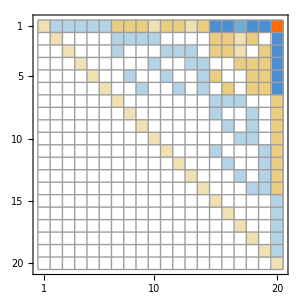
{-Graphics-{-Graphics-0,1},-Graphics-{-Graphics-1,15},-Graphics-{-Graphics-4,105},-Graphics-{-Graphics-13,20},-Graphics-{-Graphics-31,435},-Graphics-{-Graphics-40,240},-Graphics-{-Graphics-120,45},-Graphics-{-Graphics-121,90},-Graphics-{-Graphics-364,15},-Graphics-{-Graphics-760,1080},-Graphics-{-Graphics-769,1140},-Graphics-{-Graphics-849,405},-Graphics-{-Graphics-3190,100},-Graphics-{-Graphics-850,810},-Graphics-{-Graphics-3195,72},-Graphics-{-Graphics-1093,135},-Graphics-{-Graphics-3196,360},-Graphics-{-Graphics-59809,1296},-Graphics-{-Graphics-3036,420},-Graphics-{-Graphics-3037,60},-Graphics-{-Graphics-3279,180},-Graphics-{-Graphics-3280,2340},-Graphics-{-Graphics-9832,90},-Graphics-{-Graphics-9841,60},-Graphics-{-Graphics-59898,1080},-Graphics-{-Graphics-62239,540},-Graphics-{-Graphics-29524,2166},-Graphics-{-Graphics-62244,360},-Graphics-{-Graphics-243810,60},-Graphics-{-Graphics-60142,540},-Graphics-{-Graphics-62245,1800},-Graphics-{-Graphics-239386,360},-Graphics-{-Graphics-62085,2100},-Graphics-{-Graphics-243811,360},-Graphics-{-Graphics-62086,300},-Graphics-{-Graphics-243837,180},-Graphics-{-Graphics-263443,60},-Graphics-{-Graphics-62328,900},-Graphics-{-Graphics-239391,180},-Graphics-{-Graphics-62329,1440},-Graphics-{-Graphics-243838,720},-Graphics-{-Graphics-239392,180},-Graphics-{-Graphics-68881,450},-Graphics-{-Graphics-263448,180},-Graphics-{-Graphics-239394,1200},-Graphics-{-Graphics-239395,360},-Graphics-{-Graphics-68890,660},-Graphics-{-Graphics-263451,180},-Graphics-{-Graphics-239232,15},-Graphics-{-Graphics-239233,15},-Graphics-{-Graphics-246024,90},-Graphics-{-Graphics-263449,360},-Graphics-{-Graphics-243847,720},-Graphics-{-Graphics-246025,180},-Graphics-{-Graphics-88573,30},-Graphics-{-Graphics-263452,720},-Graphics-{-Graphics-243850,450},-Graphics-{-Graphics-239475,90},-Graphics-{-Graphics-239476,90},-Graphics-{-Graphics-246027,360},-Graphics-{-Graphics-263506,420},-Graphics-{-Graphics-246028,360},-Graphics-{-Graphics-790510,72},-Graphics-{-Graphics-263532,360},-Graphics-{-Graphics-790356,45},-Graphics-{-Graphics-246036,180},-Graphics-{-Graphics-790357,45},-Graphics-{-Graphics-263533,720},-Graphics-{-Graphics-246037,190},-Graphics-{-Graphics-265719,480},-Graphics-{-Graphics-265720,60},-Graphics-{-Graphics-790599,180},-Graphics-{-Graphics-777469,60},-Graphics-{-Graphics-797149,90},-Graphics-{-Graphics-790600,180},-Graphics-{-Graphics-777478,20},-Graphics-{-Graphics-797152,180},-Graphics-{-Graphics-2391240,15},-Graphics-{-Graphics-797161,60},-Graphics-{-Graphics-2391241,45},-Graphics-{-Graphics-2391484,15},-Graphics-{-Graphics-7174453,1}}

```mathematica
With[{sets=allGraphs6, max=6,colofour="colofourrealnull"},Map[
Labeled[MatrixPlot[MobiusMatrixFromSets[Map[SymbolToSets,Sort[ListofVars[sets[#[[1]],colofour]],CompareSymbols]]],Mesh->All, ImageSize->300],{Labeled[sets[#[[1]],"graph"],#[[1]]],#[[2]]}]&,
Sort[Tally[Table[k,{k,Sort[Select[Keys[sets],VertexCount[sets[#,"graph"]]==max&]]}],Length[ListofVars[sets[#1,colofour]]]==Length[ListofVars[sets[#2,colofour]]]&],Length[ListofVars[sets[#1[[1]],colofour]]]<Length[ListofVars[sets[#2[[1]],colofour]]]&]
]
]
```

```mathematica
Length[%]
```

20

```mathematica
With[{sets=allGraphs6, max=6,colofour="colofourrealnull"},Map[
Labeled[MatrixPlot[MobiusMatrixFromSets[Map[SymbolToSets,Sort[ListofVars[sets[#[[1]],colofour]],CompareSymbols]]],Mesh->All, ImageSize->300],{Labeled[sets[#[[1]],"graph"],#[[1]]],#[[2]]}]&,
{{K5Key,1}}
]
]
```

{-Graphics-{-Graphics-29524,1}}

```mathematica
With[{sets=allGraphs6, max=6,colofour="colofourrealnull"},Map[
Labeled[MatrixPlot[MobiusMatrixFromSets[Map[SymbolToSets,Sort[ListofVars[sets[#[[1]],colofour]],CompareSymbols]]],Mesh->All, ImageSize->300],{Labeled[sets[#[[1]],"graph"],#[[1]]],#[[2]]}]&,
Sort[Tally[Table[k,{k,Sort[Select[Keys[sets],MaximalPlanarQ[sets[#,"graph"]]&&VertexCount[sets[#,"graph"]]==max&]]}],Length[ListofVars[sets[#1,colofour]]]==Length[ListofVars[sets[#2,colofour]]]&]]
]
]
```

{-Graphics-{-Graphics-790600,180},-Graphics-{-Graphics-2391240,15}}